```mathematica
(* Here I am solving the ODE d^2 u[x]/d x^2 == f[x] *)
```

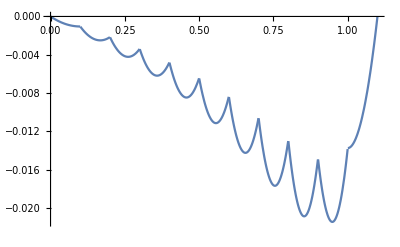

```mathematica
Block[
{f,k,m,n=10,Λ,b,v,x,u},
f[x_]:=x+x^3;
v=Table[Piecewise[{{-n^2(x-(k-1)/n)(x-(k+1)/n),(k-1)/n≤x≤(k+1)/n},{0,True}}],{k,1,n}];
Λ=Table[Table[Integrate[-D[v[[k]],x]D[v[[m]],x],{x,(k-1)/n,(k+1)/n}],{m,1,n}],{k,1,n}];
b=Table[Integrate[f[x]v[[k]],{x,(k-1)/n,(k+1)/n}],{k,1,n}];
u=Inverse[Λ].b;
Plot[Sum[u[[k]]v[[k]],{k,1,n}],{x,0,1+1/n}]
]
```

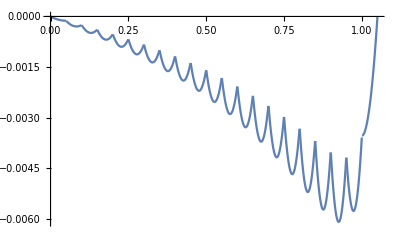

```mathematica
Block[
{f,k,m,n=20,Λ,b,v,x,u},
f[x_]:=x+x^3;
v=Table[Piecewise[{{-n^2(x-(k-1)/n)(x-(k+1)/n),(k-1)/n≤x≤(k+1)/n},{0,True}}],{k,1,n}];
Λ=Table[Table[Integrate[-D[v[[k]],x]D[v[[m]],x],{x,(k-1)/n,(k+1)/n}],{m,1,n}],{k,1,n}];
b=Table[Integrate[f[x]v[[k]],{x,(k-1)/n,(k+1)/n}],{k,1,n}];
u=Inverse[Λ].b;
Plot[Sum[u[[k]]v[[k]],{k,1,n}],{x,0,1+1/n}]
]
```

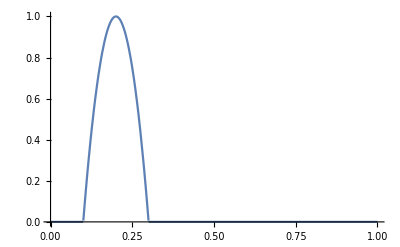

```mathematica
Block[
{n=10,k=2},
Plot[Piecewise[{{-n^2(x-(k-1)/n)(x-(k+1)/n),(k-1)/n≤x≤(k+1)/n},{0,True}}],{x,0,1},PlotRange->{{0,1},{0,1}}]
]
```

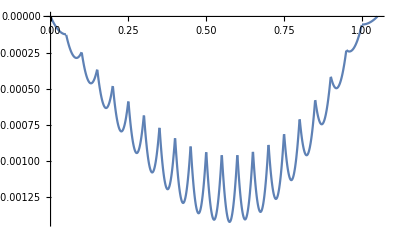

```mathematica
Block[
{f,k,m,n=20,Λ,b,v,x,u},
f[x_]:=x-x^3;
v=Table[Piecewise[{{-n^2(x-(k-1)/n)(x-(k+1)/n),(k-1)/n≤x≤(k+1)/n},{0,True}}],{k,1,n}];
Λ=Table[Table[Integrate[-D[v[[k]],x]D[v[[m]],x],{x,(k-1)/n,(k+1)/n}],{m,1,n}],{k,1,n}];
b=Table[Integrate[f[x]v[[k]],{x,(k-1)/n,(k+1)/n}],{k,1,n}];
u=Inverse[Λ].b;
Plot[Sum[u[[k]]v[[k]],{k,1,n}],{x,0,1+1/n}]
]
```

```mathematica
DSolve[D[u[x],x,x]==x-x^3,u[x],x]
```

{{u[x]→x^3/6-x^5/20+C[1]+x C[2]}}

```mathematica
Solve[1/6-1/20+C[2]==0,C[2]]
```

{{C[2]→-7/60}}

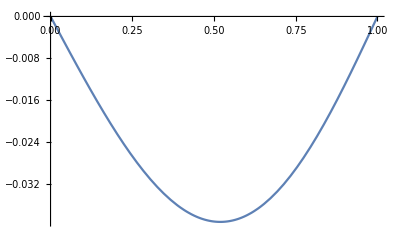

```mathematica
Plot[x^3/6-x^5/20-7/60 x,{x,0,1}]
```

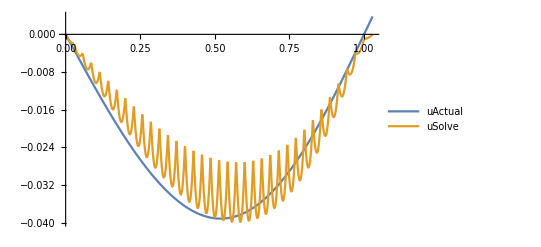

```mathematica
Block[
{f,k,m,n=35,Λ,b,v,x,u},
f[x_]:=x-x^3;
v=Table[Piecewise[{{-n^2(x-(k-1)/n)(x-(k+1)/n),(k-1)/n≤x≤(k+1)/n},{0,True}}],{k,1,n}];
Λ=Table[Table[Integrate[-D[v[[k]],x]D[v[[m]],x],{x,(k-1)/n,(k+1)/n}],{m,1,n}],{k,1,n}];
b=Table[Integrate[f[x]v[[k]],{x,(k-1)/n,(k+1)/n}],{k,1,n}];
u=Inverse[Λ].b;
Plot[{x^3/6-x^5/20-7/60 x,85Sum[u[[k]]v[[k]],{k,1,n}]},{x,0,1+1/n},PlotLegends->{"uActual","uSolve"}]
]
```

```mathematica
(* The linear tessellations for the choice of basis seems to work. *)
```

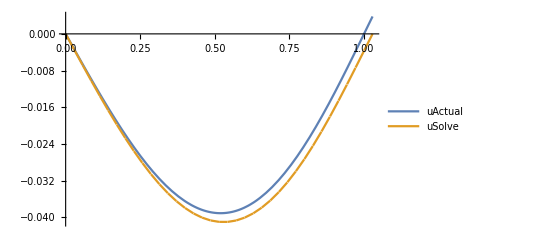

```mathematica
Block[
{f,k,m,n=35,Λ,b,v,x,u},
f[x_]:=x-x^3;
v=Table[Piecewise[{{n x-k+1,(k-1)/n≤x≤k/n},{k+1-n x,k/n≤x≤(k+1)/n},{0,True}}],{k,1,n}];
Λ=Table[Table[Integrate[-D[v[[k]],x]D[v[[m]],x],{x,(k-1)/n,(k+1)/n}],{m,1,n}],{k,1,n}];
b=Table[Integrate[f[x]v[[k]],{x,(k-1)/n,(k+1)/n}],{k,1,n}];
u=Inverse[Λ].b;
Plot[{x^3/6-x^5/20-7/60 x,Sum[u[[k]]v[[k]],{k,1,n}]},{x,0,1+1/n},PlotLegends->{"uActual","uSolve"}]
]
```

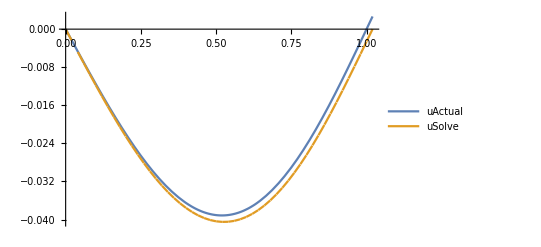

```mathematica
Block[
{f,k,m,n=50,Λ,b,v,x,u},
f[x_]:=x-x^3;
v=Table[Piecewise[{{n x-k+1,(k-1)/n≤x≤k/n},{k+1-n x,k/n≤x≤(k+1)/n},{0,True}}],{k,1,n}];
Λ=Table[Table[Integrate[-D[v[[k]],x]D[v[[m]],x],{x,(k-1)/n,(k+1)/n}],{m,1,n}],{k,1,n}];
b=Table[Integrate[f[x]v[[k]],{x,(k-1)/n,(k+1)/n}],{k,1,n}];
u=Inverse[Λ].b;
Plot[{x^3/6-x^5/20-7/60 x,Sum[u[[k]]v[[k]],{k,1,n}]},{x,0,1+1/n},PlotLegends->{"uActual","uSolve"}]
]
```

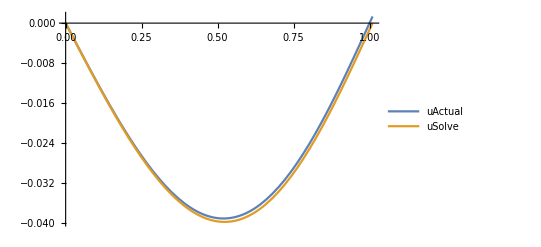

```mathematica
Block[
{f,k,m,n=100,Λ,b,v,x,u},
f[x_]:=x-x^3;
v=Table[Piecewise[{{n x-k+1,(k-1)/n≤x≤k/n},{k+1-n x,k/n≤x≤(k+1)/n},{0,True}}],{k,1,n}];
Λ=Table[Table[Integrate[-D[v[[k]],x]D[v[[m]],x],{x,(k-1)/n,(k+1)/n}],{m,1,n}],{k,1,n}];
b=Table[Integrate[f[x]v[[k]],{x,(k-1)/n,(k+1)/n}],{k,1,n}];
u=Inverse[Λ].b;
Plot[{x^3/6-x^5/20-7/60 x,Sum[u[[k]]v[[k]],{k,1,n}]},{x,0,1+1/n},PlotLegends->{"uActual","uSolve"}]
]
```

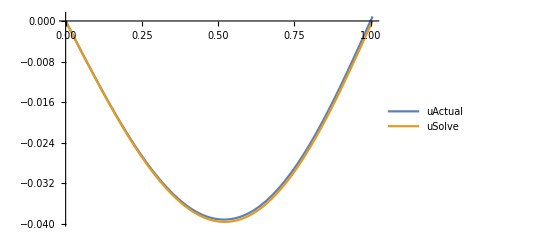

```mathematica
Block[
{f,k,m,n=150,Λ,b,v,x,u},
f[x_]:=x-x^3;
v=Table[Piecewise[{{n x-k+1,(k-1)/n≤x≤k/n},{k+1-n x,k/n≤x≤(k+1)/n},{0,True}}],{k,1,n}];
Λ=Table[Table[Integrate[-D[v[[k]],x]D[v[[m]],x],{x,(k-1)/n,(k+1)/n}],{m,1,n}],{k,1,n}];
b=Table[Integrate[f[x]v[[k]],{x,(k-1)/n,(k+1)/n}],{k,1,n}];
u=Inverse[Λ].b;
Plot[{x^3/6-x^5/20-7/60 x,Sum[u[[k]]v[[k]],{k,1,n}]},{x,0,1+1/n},PlotLegends->{"uActual","uSolve"}]
]
```

```mathematica
DSolve[D[u[x],x,x]+7 D[u[x],x]+6u[x]==10x,u[x],x]
```

{{u[x]→5/18 (-7+6 x)+ⅇ^(-6 x) C[1]+ⅇ^-x C[2]}}

```mathematica
Solve[
{
(5/18 (-7)+C[1]+C[2])==0,
(5/18 (-7+6 E)+ⅇ^(-6 E) C[1]+ⅇ^-E C[2])==0
},
{C[1],C[2]}
]
```

{{C[1]→(5 ⅇ^(5 ⅇ) (7-7 ⅇ^ⅇ+6 ⅇ^(1+ⅇ)))/(18 (-1+ⅇ^(5 ⅇ))),C[2]→-(5 (7-7 ⅇ^(6 ⅇ)+6 ⅇ^(1+6 ⅇ)))/(18 (-1+ⅇ^(5 ⅇ)))}}

```mathematica
FullSimplify[(5/18 (-7+6 x)+ⅇ^(-6 x) C[1]+ⅇ^-x C[2])/.{C[1]->(5 ⅇ^(5 ⅇ) (7-7 ⅇ^ⅇ+6 ⅇ^(1+ⅇ)))/(18 (-1+ⅇ^(5 ⅇ))),C[2]->-(5 (7-7 ⅇ^(6 ⅇ)+6 ⅇ^(1+6 ⅇ)))/(18 (-1+ⅇ^(5 ⅇ)))}]
```

(ⅇ^(-6 x) (5 ⅇ^(5 ⅇ) (7+ⅇ^ⅇ (-7+6 ⅇ))-5 ⅇ^(5 x) (7+ⅇ^(6 ⅇ) (-7+6 ⅇ))+5 ⅇ^(6 x) (-1+ⅇ^(5 ⅇ)) (-7+6 x)))/(18 (-1+ⅇ^(5 ⅇ)))

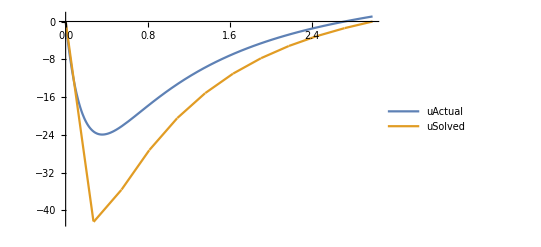

```mathematica
Block[
{f,k,m,n=10,Λ,b,v,x,u},
f[x_]:=10x;
v=Table[Piecewise[{{n x/E-k+1,(k-1)E/n≤x≤k E/n},{k+1-n x/E,k E/n≤x≤(k+1)E/n},{0,True}}],{k,1,n}];
Λ=Table[Table[Integrate[6v[[m]]v[[k]]-D[v[[m]],x]D[v[[k]],x]-7 v[[m]]D[v[[k]],x],{x,(k-1)E/n,(k+1)E/n}],{m,1,n}],{k,1,n}];
b=Table[Integrate[f[x]v[[k]],{x,(k-1)E/n,(k+1)E/n}],{k,1,n}];
u=Inverse[Λ].b;
Plot[{(ⅇ^(-6 x) (5 ⅇ^(5 ⅇ) (7+ⅇ^ⅇ (-7+6 ⅇ))-5 ⅇ^(5 x) (7+ⅇ^(6 ⅇ) (-7+6 ⅇ))+5 ⅇ^(6 x) (-1+ⅇ^(5 ⅇ)) (-7+6 x)))/(18 (-1+ⅇ^(5 ⅇ))),Sum[u[[k]]v[[k]],{k,1,n}]},{x,0,E(1+1/n)},PlotLegends->{"uActual","uSolved"}]
]
```

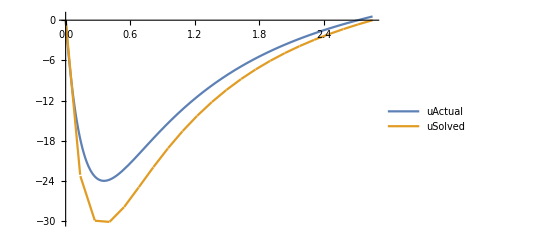

```mathematica
Block[
{f,k,m,n=20,Λ,b,v,x,u},
f[x_]:=10x;
v=Table[Piecewise[{{n x/E-k+1,(k-1)E/n≤x≤k E/n},{k+1-n x/E,k E/n≤x≤(k+1)E/n},{0,True}}],{k,1,n}];
Λ=Table[Table[Integrate[6v[[m]]v[[k]]-D[v[[m]],x]D[v[[k]],x]-7 v[[m]]D[v[[k]],x],{x,(k-1)E/n,(k+1)E/n}],{m,1,n}],{k,1,n}];
b=Table[Integrate[f[x]v[[k]],{x,(k-1)E/n,(k+1)E/n}],{k,1,n}];
u=Inverse[Λ].b;
Plot[{(ⅇ^(-6 x) (5 ⅇ^(5 ⅇ) (7+ⅇ^ⅇ (-7+6 ⅇ))-5 ⅇ^(5 x) (7+ⅇ^(6 ⅇ) (-7+6 ⅇ))+5 ⅇ^(6 x) (-1+ⅇ^(5 ⅇ)) (-7+6 x)))/(18 (-1+ⅇ^(5 ⅇ))),Sum[u[[k]]v[[k]],{k,1,n}]},{x,0,E(1+1/n)},PlotLegends->{"uActual","uSolved"}]
]
```

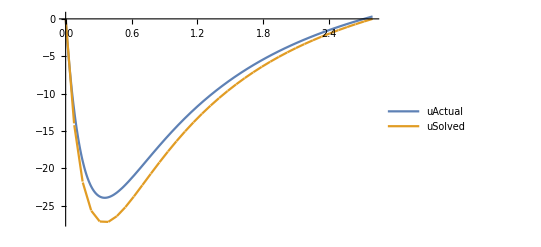

```mathematica
Block[
{f,k,m,n=35,Λ,b,v,x,u},
f[x_]:=10x;
v=Table[Piecewise[{{n x/E-k+1,(k-1)E/n≤x≤k E/n},{k+1-n x/E,k E/n≤x≤(k+1)E/n},{0,True}}],{k,1,n}];
Λ=Table[Table[Integrate[6v[[m]]v[[k]]-D[v[[m]],x]D[v[[k]],x]-7 v[[m]]D[v[[k]],x],{x,(k-1)E/n,(k+1)E/n}],{m,1,n}],{k,1,n}]//N;
b=Table[Integrate[f[x]v[[k]],{x,(k-1)E/n,(k+1)E/n}],{k,1,n}]//N;
u=Inverse[Λ].b;
Plot[{(ⅇ^(-6 x) (5 ⅇ^(5 ⅇ) (7+ⅇ^ⅇ (-7+6 ⅇ))-5 ⅇ^(5 x) (7+ⅇ^(6 ⅇ) (-7+6 ⅇ))+5 ⅇ^(6 x) (-1+ⅇ^(5 ⅇ)) (-7+6 x)))/(18 (-1+ⅇ^(5 ⅇ))),Sum[u[[k]]v[[k]],{k,1,n}]},{x,0,E(1+1/n)},PlotLegends->{"uActual","uSolved"}]
]
```

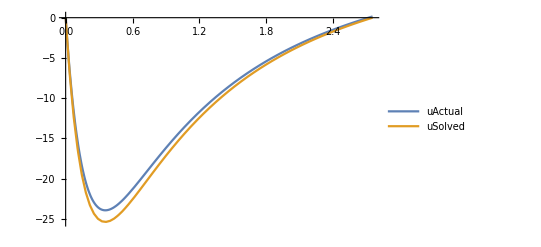

```mathematica
Block[
{f,k,m,n=75,Λ,b,v,x,u},
f[x_]:=10x;
v=Table[Piecewise[{{n x/E-k+1,(k-1)E/n≤x≤k E/n},{k+1-n x/E,k E/n≤x≤(k+1)E/n},{0,True}}],{k,1,n}];
Λ=Table[Table[Integrate[6v[[m]]v[[k]]-D[v[[m]],x]D[v[[k]],x]-7 v[[m]]D[v[[k]],x],{x,(k-1)E/n,(k+1)E/n}],{m,1,n}],{k,1,n}]//N;
b=Table[Integrate[f[x]v[[k]],{x,(k-1)E/n,(k+1)E/n}],{k,1,n}]//N;
u=Inverse[Λ].b;
Plot[{(ⅇ^(-6 x) (5 ⅇ^(5 ⅇ) (7+ⅇ^ⅇ (-7+6 ⅇ))-5 ⅇ^(5 x) (7+ⅇ^(6 ⅇ) (-7+6 ⅇ))+5 ⅇ^(6 x) (-1+ⅇ^(5 ⅇ)) (-7+6 x)))/(18 (-1+ⅇ^(5 ⅇ))),Sum[u[[k]]v[[k]],{k,1,n}]},{x,0,E(1+1/n)},PlotLegends->{"uActual","uSolved"}]
]
```